## Phi3 Number Visibility

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
series=(100#1+10#2+#3)&@@@Partition[RealDigits[GoldenRatio,10,30002][[1,2;;]],3];
```

## SDL Complexity

```mathematica
<<sdl.mx
```

```mathematica
result=sdl[series]
```

{0.0966967,0.975211}

## Visibility

```mathematica
<<visibility.mx
```

```mathematica
links=naturalVisibilityLinks[series];
```

```mathematica
natGraph=Graph[links, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[natGraph]//Mean//N]
```

```mathematica
count=VertexDegree[natGraph]//Counts
```

<|1→1,27→14,2→2260,4→1547,7→516,6→675,8→373,15→74,9→295,12→161,24→18,21→29,20→27,19→36,11→188,22→19,26→15,30→4,40→3,3→2056,5→1033,10→226,14→99,13→99,16→51,17→60,18→56,23→18,25→15,33→3,36→2,32→3,37→3,29→8,44→1,39→1,28→4,35→1,47→1,34→1,31→3|>

```mathematica
If[count[1]<3,count[1]=.];
```

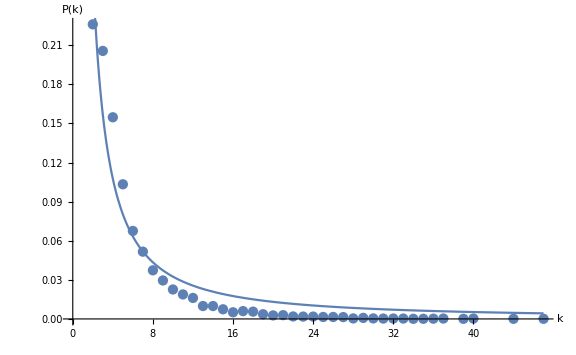
{{C→0.659132,γ→1.30811},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```

{{0.2192,0.941814},{{0.0132326,0.00460448},{1.264,0.299422}},{{0.0282261,0.00496735},{1.78439,0.190429}}}

## Horizontal Visibility

```mathematica
horlinks=horizontalVisibilityLinks[series];
```

```mathematica
hg=Graph[horlinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[hg]//Mean//N]
```

```mathematica
count=VertexDegree[hg]//Counts
```

<|1→1,11→98,2→3617,4→1325,7→456,10→129,13→45,16→12,14→38,15→23,3→2131,5→921,6→600,8→292,12→65,9→220,18→5,19→5,17→13,21→1,20→2|>

```mathematica
If[count[1]<3,count[1]=.];
```

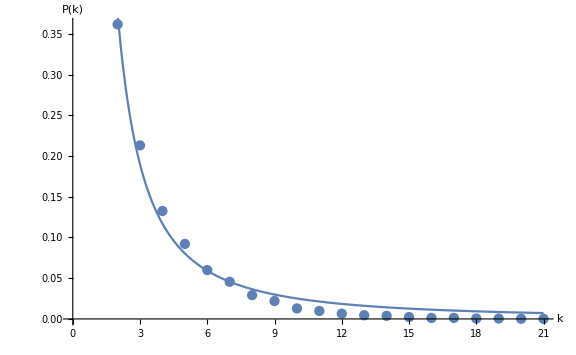
{{C→1.20273,γ→1.68099},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```

{{0.2192,0.941814},{{0.0132326,0.00460448},{1.264,0.299422}},{{0.0282261,0.00496735},{1.78439,0.190429}}}